```mathematica
τ=0.1;
dd=X;
ddy=y;
cc=0.5;
```

```mathematica
KernelMatrix[K_,X_]:=Outer[K,X,X,1];    
IdentityKernel[x_,y_]:=x.y;
PolynomialKernel[x_,y_,d_Integer]:=(x.y+1)^d;
pk=PolynomialKernel[#1,#2,2]&;
    l=Length[dd];
qp=
      {KernelMatrix[pk,dd]*Outer[Times,ddy,ddy],
        Table[-1,{l}],
        Table[0,{l}],
        Table[cc,{l}],
        0,
        y,
        τ};
```

```mathematica
Dimensions[qp[[1]]]
```

{83,83}

```mathematica
xx=Table[Subscript[x, i],{i,Length[qp[[1]]]}]
Cond=Table[Subscript[x, i]>=0 ,{i,Length[qp[[1]]]}]
```

{x_1,x_2,x_3,x_4,x_5,x_6,x_7,x_8,x_9,x_10,x_11,x_12,x_13,x_14,x_15,x_16,x_17,x_18,x_19,x_20,x_21,x_22,x_23,x_24,x_25,x_26,x_27,x_28,x_29,x_30,x_31,x_32,x_33,x_34,x_35,x_36,x_37,x_38,x_39,x_40,x_41,x_42,x_43,x_44,x_45,x_46,x_47,x_48,x_49,x_50,x_51,x_52,x_53,x_54,x_55,x_56,x_57,x_58,x_59,x_60,x_61,x_62,x_63,x_64,x_65,x_66,x_67,x_68,x_69,x_70,x_71,x_72,x_73,x_74,x_75,x_76,x_77,x_78,x_79,x_80,x_81,x_82,x_83}

{x_1≥0,x_2≥0,x_3≥0,x_4≥0,x_5≥0,x_6≥0,x_7≥0,x_8≥0,x_9≥0,x_10≥0,x_11≥0,x_12≥0,x_13≥0,x_14≥0,x_15≥0,x_16≥0,x_17≥0,x_18≥0,x_19≥0,x_20≥0,x_21≥0,x_22≥0,x_23≥0,x_24≥0,x_25≥0,x_26≥0,x_27≥0,x_28≥0,x_29≥0,x_30≥0,x_31≥0,x_32≥0,x_33≥0,x_34≥0,x_35≥0,x_36≥0,x_37≥0,x_38≥0,x_39≥0,x_40≥0,x_41≥0,x_42≥0,x_43≥0,x_44≥0,x_45≥0,x_46≥0,x_47≥0,x_48≥0,x_49≥0,x_50≥0,x_51≥0,x_52≥0,x_53≥0,x_54≥0,x_55≥0,x_56≥0,x_57≥0,x_58≥0,x_59≥0,x_60≥0,x_61≥0,x_62≥0,x_63≥0,x_64≥0,x_65≥0,x_66≥0,x_67≥0,x_68≥0,x_69≥0,x_70≥0,x_71≥0,x_72≥0,x_73≥0,x_74≥0,x_75≥0,x_76≥0,x_77≥0,x_78≥0,x_79≥0,x_80≥0,x_81≥0,x_82≥0,x_83≥0}

x_1≥0

```mathematica
f=0.5xx.qp[[1]].xx+qp[[2]].xx;
```

```mathematica
Dimensions[qp[[2]].xx]
```

{83}

{1,1,-1,-1}

```mathematica
NMinimize[{f,
   Subscript[x, 1]≥0And Subscript[x, 2]≥0And Subscript[x, 3]≥0And Subscript[x, 4]≥0And Subscript[x, 5]≥0And Subscript[x, 6]≥0And Subscript[x, 7]≥0And Subscript[x, 8]≥0And Subscript[x, 9]≥0And Subscript[x, 10]≥0And Subscript[x, 11]≥0And Subscript[x, 12]≥0And Subscript[x, 13]≥0And Subscript[x, 14]≥0And Subscript[x, 15]≥0And Subscript[x, 16]≥0And Subscript[x, 17]≥0And Subscript[x, 18]≥0And Subscript[x, 19]≥0And Subscript[x, 20]≥0And Subscript[x, 21]≥0And Subscript[x, 22]≥0And Subscript[x, 23]≥0And Subscript[x, 24]≥0And Subscript[x, 25]≥0And Subscript[x, 26]≥0And Subscript[x, 27]≥0And Subscript[x, 28]≥0And Subscript[x, 29]≥0And Subscript[x, 30]≥0And Subscript[x, 31]≥0And Subscript[x, 32]≥0And Subscript[x, 33]≥0And Subscript[x, 34]≥0And Subscript[x, 35]≥0And Subscript[x, 36]≥0And Subscript[x, 37]≥0And Subscript[x, 38]≥0And Subscript[x, 39]≥0And Subscript[x, 40]≥0And Subscript[x, 41]≥0And Subscript[x, 42]≥0And Subscript[x, 43]≥0And Subscript[x, 44]≥0And Subscript[x, 45]≥0And Subscript[x, 46]≥0And Subscript[x, 47]≥0And Subscript[x, 48]≥0And Subscript[x, 49]≥0And Subscript[x, 50]≥0And Subscript[x, 51]≥0And Subscript[x, 52]≥0And Subscript[x, 53]≥0And Subscript[x, 54]≥0And Subscript[x, 55]≥0And Subscript[x, 56]≥0And Subscript[x, 57]≥0And Subscript[x, 58]≥0And Subscript[x, 59]≥0And Subscript[x, 60]≥0And Subscript[x, 61]≥0And Subscript[x, 62]≥0And Subscript[x, 63]≥0And Subscript[x, 64]≥0And Subscript[x, 65]≥0And Subscript[x, 66]≥0And Subscript[x, 67]≥0And Subscript[x, 68]≥0And Subscript[x, 69]≥0And Subscript[x, 70]≥0And Subscript[x, 71]≥0And Subscript[x, 72]≥0And Subscript[x, 73]≥0And Subscript[x, 74]≥0And Subscript[x, 75]≥0And Subscript[x, 76]≥0And Subscript[x, 77]≥0And Subscript[x, 78]≥0And Subscript[x, 79]≥0And Subscript[x, 80]≥0And Subscript[x, 81]≥0And Subscript[x, 82]≥0And Subscript[x, 83]≥0 And qp[[6]].xx==0},
xx,AccuracyGoal->5(*Method->"DifferentialEvolution"*)]//Timing
```

{47.219,{555916.,{x_1→0.0000215989,x_2→0.00020188,x_3→0.00117268,x_4→-6.43135×10^-6,x_5→-1.10279×10^-6,x_6→0.000166406,x_7→-0.000936331,x_8→-0.000399386,x_9→-0.0000156707,x_10→0.0000368259,x_11→0.000203833,x_12→-0.000065251,x_13→-0.000151154,x_14→0.000238535,x_15→-0.000167825,x_16→0.000169953,x_17→-0.000114373,x_18→0.0000645681,x_19→0.00026058,x_20→0.000201361,x_21→-0.000102784,x_22→0.00014874,x_23→0.0000372899,x_24→0.0000916149,x_25→0.000784411,x_26→0.00192668,x_27→-0.00268234,x_28→-0.000256113,x_29→0.000371022,x_30→-0.000701714,x_31→0.00123007,x_32→0.000570002,x_33→0.000109704,x_34→-0.00369554,x_35→-0.000494654,x_36→-0.0000727751,x_37→-0.00159667,x_38→0.000509448,x_39→0.000256128,x_40→-0.000473923,x_41→-0.00621709,x_42→-0.0000417553,x_43→-0.000386445,x_44→-0.0000578893,x_45→-0.00383995,x_46→0.000318086,x_47→0.00255532,x_48→0.00338922,x_49→0.00203557,x_50→-0.00192061,x_51→0.0000251941,x_52→-0.00179661,x_53→-0.00236746,x_54→0.0000787881,x_55→-0.000585393,x_56→-0.00502722,x_57→-0.00068528,x_58→-0.00570469,x_59→0.000213253,x_60→0.000166514,x_61→0.00318862,x_62→0.00300135,x_63→0.000272911,x_64→-0.0193606,x_65→0.0014634,x_66→0.0259429,x_67→-0.002115,x_68→-0.0280153,x_69→-0.0376194,x_70→-0.0000743497,x_71→-0.0304484,x_72→0.00107553,x_73→0.00785505,x_74→0.000276191,x_75→0.00479986,x_76→0.147153,x_77→-0.00159914,x_78→0.0000905218,x_79→-0.03843,x_80→0.000620697,x_81→-0.000649291,x_82→1.08865×10^-7,x_83→0.0182685}}}

```mathematica
sol=%;
```

```mathematica
qp[[6]].xx/.sol[[2,2]]
```

-0.0514433

```mathematica
sxx=xx/.sol[[2,2]];
```

```mathematica
w=  Sum[ddy[[i]]*sxx[[
        i]]*dd[[i]],{i,
      Length[dd]}];
```

```mathematica
Clear[Subscript[dx, 1],Subscript[dx, 2],Subscript[dx, 3],Subscript[dx, 4],Subscript[dx, 5],Subscript[dx, 6],Subscript[dx, 7],Subscript[dx, 8],Subscript[dx, 9],Subscript[dx, 10],Subscript[dx, 11],Subscript[dx, 12],Subscript[dx, 13],Subscript[dx, 14],Subscript[dx, 15],Subscript[dx, 16],Subscript[dx, 17],Subscript[dx, 18],Subscript[dx, 19],Subscript[dx, 20],Subscript[dx, 21],Subscript[dx, 22],Subscript[dx, 23],Subscript[dx, 24],Subscript[dx, 25],Subscript[dx, 26],Subscript[dx, 27],Subscript[dx, 28],Subscript[dx, 29],Subscript[dx, 30],Subscript[dx, 31],Subscript[dx, 32],Subscript[dx, 33],Subscript[dx, 34],Subscript[dx, 35],Subscript[dx, 36],Subscript[dx, 37],Subscript[dx, 38],Subscript[dx, 39],Subscript[dx, 40],Subscript[dx, 41],Subscript[dx, 42],Subscript[dx, 43],Subscript[dx, 44],Subscript[dx, 45],Subscript[dx, 46],Subscript[dx, 47],Subscript[dx, 48],Subscript[dx, 49],Subscript[dx, 50],Subscript[dx, 51],Subscript[dx, 52],Subscript[dx, 53],Subscript[dx, 54],Subscript[dx, 55],Subscript[dx, 56],Subscript[dx, 57],Subscript[dx, 58],Subscript[dx, 59],Subscript[dx, 60],Subscript[dx, 61],Subscript[dx, 62],Subscript[dx, 63],Subscript[dx, 64],Subscript[dx, 65],Subscript[dx, 66],Subscript[dx, 67],Subscript[dx, 68],Subscript[dx, 69],Subscript[dx, 70],Subscript[dx, 71],Subscript[dx, 72],Subscript[dx, 73],Subscript[dx, 74],Subscript[dx, 75],Subscript[dx, 76],Subscript[dx, 77],Subscript[dx, 78],Subscript[dx, 79],Subscript[dx, 80],Subscript[dx, 81],Subscript[dx, 82],Subscript[dx, 83],Subscript[dx, 84],Subscript[dx, 85],Subscript[dx, 86],Subscript[dx, 87],Subscript[dx, 88],Subscript[dx, 89],Subscript[dx, 90],Subscript[dx, 91],Subscript[dx, 92]];
dxx=Table[Subscript[dx, i],{i,Length[dd[[1]]]}];
```

Clear::ssym: dx_1 is not a symbol or a string.

Clear::ssym: dx_2 is not a symbol or a string.

Clear::ssym: dx_3 is not a symbol or a string.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
wpk= Sum[sxx[[i]]*y[[i]]*Map[pk[dxx,#]&,dd],{i,
      Length[dd]}];
Dimensions[wpk]
```

{83}

```mathematica
wpk
```

{-2.22285×10^14,-5.75812×10^12,-1.5318×10^12,-9.4514×10^13,-1.10345×10^14,-7.63682×10^13,-7.31477×10^13,-6.31217×10^12,-1.52103×10^14,-6.52563×10^13,-4.11011×10^12,-4.8536×10^12,-5.52487×10^13,-4.90496×10^12,-1.50304×10^14,-2.12606×10^14,-1.0384×10^14,-4.09045×10^13,-4.47141×10^13,-3.35782×10^13,-4.4233×10^13,-1.50496×10^14,-1.20049×10^14,-2.91733×10^13,-4.54693×10^12,-3.13954×10^12,-2.56703×10^12,-2.38064×10^14,-2.0295×10^14,-4.35205×10^11,-4.59108×10^12,-9.97421×10^12,-5.40959×10^13,-2.39619×10^12,-3.26338×10^12,-1.26488×10^13,-1.09281×10^12,-1.10291×10^13,-6.26638×10^12,-4.0872×10^12,-8.80993×10^11,-4.63334×10^13,-2.47002×10^12,-3.17803×10^11,-2.83492×10^11,-1.34318×10^12,-1.46099×10^12,-3.95101×10^10,-9.28697×10^11,-1.4842×10^11,-5.76745×10^13,-4.36167×10^11,-1.81331×10^11,-1.58188×10^12,-8.07428×10^11,-8.06738×10^10,-2.49393×10^12,-2.02579×10^11,-1.87162×10^12,-5.38679×10^11,-5.98702×10^10,-1.03993×10^12,-5.25644×10^10,-1.05698×10^11,-2.42693×10^12,-8.4383×10^10,-1.62008×10^11,-3.12664×10^11,-2.73239×10^10,-1.73722×10^12,-1.03519×10^11,-3.00374×10^11,-3.15928×10^11,-1.42006×10^12,-4.28564×10^11,-7.84292×10^10,-3.78178×10^10,-5.63016×10^11,-1.02567×10^11,-3.77602×10^11,-3.90005×10^11,-2.81037×10^14,-1.29854×10^11}

```mathematica
Dimensions[w]
```

{92}

```mathematica
w;
```

```mathematica
(*wpk[[1]]*)

{Subscript[dx, 1],Subscript[dx, 2],Subscript[dx, 3],Subscript[dx, 4],Subscript[dx, 5],Subscript[dx, 6],Subscript[dx, 7],Subscript[dx, 8],Subscript[dx, 9],Subscript[dx, 10],Subscript[dx, 11],Subscript[dx, 12],Subscript[dx, 13],Subscript[dx, 14],Subscript[dx, 15],Subscript[dx, 16],Subscript[dx, 17],Subscript[dx, 18],Subscript[dx, 19],Subscript[dx, 20],Subscript[dx, 21],Subscript[dx, 22],Subscript[dx, 23],Subscript[dx, 24],Subscript[dx, 25],Subscript[dx, 26],Subscript[dx, 27],Subscript[dx, 28],Subscript[dx, 29],Subscript[dx, 30],Subscript[dx, 31],Subscript[dx, 32],Subscript[dx, 33],Subscript[dx, 34],Subscript[dx, 35],Subscript[dx, 36],Subscript[dx, 37],Subscript[dx, 38],Subscript[dx, 39],Subscript[dx, 40],Subscript[dx, 41],Subscript[dx, 42],Subscript[dx, 43],Subscript[dx, 44],Subscript[dx, 45],Subscript[dx, 46],Subscript[dx, 47],Subscript[dx, 48],Subscript[dx, 49],Subscript[dx, 50],Subscript[dx, 51],Subscript[dx, 52],Subscript[dx, 53],Subscript[dx, 54],Subscript[dx, 55],Subscript[dx, 56],Subscript[dx, 57],Subscript[dx, 58],Subscript[dx, 59],Subscript[dx, 60],Subscript[dx, 61],Subscript[dx, 62],Subscript[dx, 63],Subscript[dx, 64],Subscript[dx, 65],Subscript[dx, 66],Subscript[dx, 67],Subscript[dx, 68],Subscript[dx, 69],Subscript[dx, 70],Subscript[dx, 71],Subscript[dx, 72],Subscript[dx, 73],Subscript[dx, 74],Subscript[dx, 75],Subscript[dx, 76],Subscript[dx, 77],Subscript[dx, 78],Subscript[dx, 79],Subscript[dx, 80],Subscript[dx, 81],Subscript[dx, 82],Subscript[dx, 83],Subscript[dx, 84],Subscript[dx, 85],Subscript[dx, 86],Subscript[dx, 87],Subscript[dx, 88],Subscript[dx, 89],Subscript[dx, 90],Subscript[dx, 91],Subscript[dx, 92]}=dd[[1]];
Subscript[dx, 1]
```

1821.29

```mathematica
Select[sxx,#-Mean[sxx]>2StandardDeviation[sxx]&]
```

{0.147153}

```mathematica
sv1=Ordering[sxx,-70];
```

```mathematica
sy=y[[sv1]]
  
    sv={Position[sxx*y,_?Positive]//Flatten,
 Position[sxx*y,_?Negative]//Flatten};
```

{-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,1,-1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
sv
```

{{1,2,3,6,10,11,14,16,18,19,20,22,23,24,25,26,29,31,32,33,38,39,42,43,44,45,50,52,53,55,56,57,58,64,67,68,69,70,71,77,79,81},{4,5,7,8,9,12,13,15,17,21,27,28,30,34,35,36,37,40,41,46,47,48,49,51,54,59,60,61,62,63,65,66,72,73,74,75,76,78,80,82,83}}

```mathematica
Length[dd]
Length[w]
```

83

92

```mathematica
Bias= Mean[-w.Transpose[dd]];

Biask= Mean[-wpk/.](*-(Sum[w.dd[[     sv[[1]]  ]][[i]],{i,Length[sv[[1]]]}  ]+    Sum[w .dd[[     sv[[2]]  ]][[i]], {i,Length[sv[[2]]]}])/2*)
```

26182.

```mathematica
rs=Map[w.#+Bias&,dd]
rsx=Map[w.#&,dd];
```

{-65768.3,9242.62,13892.5,-51666.9,-55497.4,-46424.,-43383.7,11781.3,-37337.,-8088.75,11136.5,12835.7,-33075.1,11012.3,-64737.5,-88471.,-39358.8,-7012.3,-29193.4,-9954.45,-41988.6,-82015.1,-48015.,629.551,9846.78,12921.1,14404.,-108059.,-94612.2,21045.6,4951.19,5373.47,-33865.6,13965.7,19298.5,-7717.91,21544.7,-2509.24,70.392,9966.23,18877.5,-17172.3,13690.5,23035.1,21303.9,19054.1,19287.2,24960.3,18611.2,24061.1,-14603.9,20751.1,23930.7,19191.3,21534.7,24029.8,16865.7,22755.6,18837.2,21221.7,25028.2,18984.2,24456.2,23236.9,17550.,23590.,24600.6,22632.4,25234.1,17517.1,23763.2,22699.4,21887.2,14470.4,22147.1,23456.9,25173.5,20846.1,23520.3,23346.8,20611.2,-32902.5,22761.2}

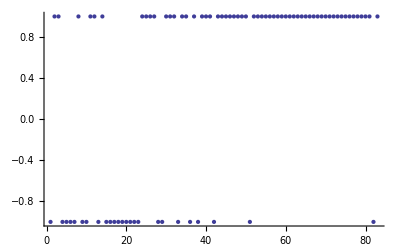

```mathematica
ListPlot[Sign[rs]]
```

```mathematica
N[HammingDistance[Sign[rs],y]/Length[y]]
```

0.73494

```mathematica
α*y*Map[K[{x1,x2},#]&,X]
```

{6.66688×10^8,-1.89808×10^7,-2.3063×10^8,7.20786×10^8,8.71119×10^8,8.11367×10^8,7.63329×10^8,-2.98798×10^8,9.6107×10^7,-4.99165×10^7,-1.6987×10^8,-2.77598×10^8,4.19683×10^8,-1.8673×10^8,9.11129×10^8,1.25352×10^9,7.68963×10^8,3.14997×10^8,3.11482×10^8,1.01419×10^8,5.98109×10^8,1.2007×10^9,7.09368×10^8,-7.37443×10^7,-1.60601×10^8,-1.99115×10^8,-3.28346×10^8,1.38193×10^9,1.26375×10^9,-3.98343×10^8,-1.65879×10^8,-1.46018×10^8,4.13211×10^8,-1.47671×10^8,-2.84739×10^8,-3.67652×10^7,-3.56185×10^8,1.52539×10^7,-6.19581×10^7,1.57858×10^9,1.38104×10^9,-5.02904×10^7,-3.46611×10^8,-4.14613×10^8,-4.10571×10^8,-3.80665×10^8,-3.77859×10^8,-4.33594×10^8,-3.85565×10^8,-4.23887×10^8,-2.92212×10^7,-4.04386×10^8,-4.21134×10^8,-3.75307×10^8,-3.95023×10^8,-4.28278×10^8,-3.55349×10^8,-4.18032×10^8,-3.68367×10^8,-4.0337×10^8,-4.32328×10^8,-3.84583×10^8,-4.31287×10^8,-4.24247×10^8,-3.582×10^8,-4.26715×10^8,-4.25459×10^8,-4.1312×10^8,-4.35556×10^8,-3.67694×10^8,-4.25266×10^8,-4.13554×10^8,-4.10721×10^8,-3.66186×10^8,-4.07691×10^8,-4.27352×10^8,-4.34584×10^8,-4.00785×10^8,-4.24994×10^8,-4.12378×10^8,-4.06003×10^8,4.47914×10^8,-4.22526×10^8}

```mathematica
HammingDistance[Sign[rs2],y2]
```

20